```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["like_data.csv"];
(* Remove the last "empty" data cell *)
names=data[[1,2;;]];
times=data[[2;;,1]];
data=data[[2;;,2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data[[j]]]<i,
StringLength[ToString[data[[j,i]]]]==0],
InvalidNum,data[[j,i]]]

,{i,Length[names]}],{j,Length[data]}];
data=emptyData;


lastNamesWithParty=(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names;
lastNamesWithoutParty=(split=StringSplit[#];split[[2]])&/@names;
Clear[split]


(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Table[data[[i+1]]-data[[i]],{i,1,Length[data]-1}];
percentDiffData=Table[(data[[i+1]]-data[[i]])/data[[i]]//N,{i,1,Length[data]-1}];
titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};

NewCandidate[names_List,times_List,data_List,filename_String]:=Module[{ret,candidateVals},
If[Or[Length[times]≠Length[data],Length[names]≠Length[data[[1]]]],Message[NewCandidate::illegal],
ret=Table[Table["",{c,Length[names]+1}],{r,Length[times]+1}];
ret[[1,1]]="Timestamp";
ret[[1,2;;]]=names;
ret[[2;;,1]]=times;
candidateVals=Table[FirstCase[data[[All,i]],_?(#>0&)],{i,Length[names]}];

(*Update the rows that have the bad data for each of the new candidates*)
ret[[2;;,2;;]]=Table[Table[If[data[[c,r]]==InvalidNum,candidateVals[[r]],data[[c,r]]],{r,Length[names]}],{c,Length[times]}];
Export[filename,ret]
]]

findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]
(*NewCandidate[names,times,data,"like_data.csv"]*)
```

```mathematica
graphFn[option_Integer,selection_List,scale_Integer]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData]];
graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];

fn[ConvertToTimes[graph[[All,selection]],graphTimes],PlotLegends->labels[[selection]],
PlotLabel->plotLabel,
PlotRange->All]]
Manipulate[
graphFn[option,selection,scale],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}}
]
```

```mathematica
(*Export["demplot.png",Show[graphFn[1,dems,1],ImageSize->{800,800}],ImageResolution->300]*)
```

demplot.png

```mathematica
pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,If[option≤2,Length[times],Length[times]-1],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
(*Export["pie.gif",Table[Show[pieFn[1,i,Range[Length[names]]],ImageSize->{800,800}],{i,Length[times]}],"DisplayDurations"->1,ImageResolution->300]*)
```

pie.gif

```mathematica
tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
({Mean[#],StandardDeviation[#]}//N)&[absoluteDiffData[[All,19]]]
```

{36.2857,38.4136}

```mathematica
(#[[1]]-#[[2]])&/@data[[All,{3,5}]]
```

{275567,271750,272932,273954,271783,268264,263442,259983,256966,253795,250717,246060,239447,237657,234209}

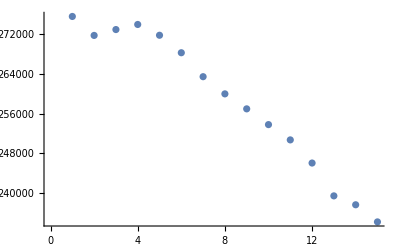

```mathematica
ListPlot[{275567,271750,272932,273954,271783,268264,263442,259983,256966,253795,250717,246060,239447,237657,234209}]
```

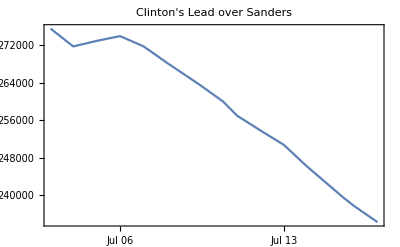

```mathematica
DateListPlot[Table[{times[[i]],data[[i,3]]-data[[i,5]]},{i,Length[data]}],PlotLabel->"Clinton's Lead over Sanders"]
```

```mathematica
NonlinearModelFit[Table[{i,data[[i,3]]-data[[i,5]]},{i,Length[data]}],a t + b, {a,b},{t}]
```

FittedModel[283340.-3113.13 t]

```mathematica
283/3//N
```

94.3333

today plus 90 days

WolframAlphaQueryResults